```mathematica
f[x_] = 1.4*Cos[3.9*x] - Log[2.5*x]
```

1.4 Cos[3.9 x]-Log[2.5 x]

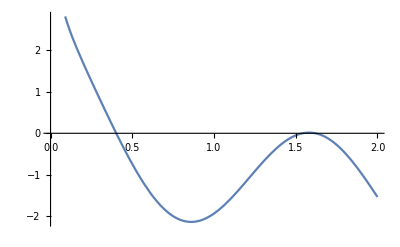

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
FindRoot[f[x],{x,0.5}]
```

{x→0.4019}

```mathematica
FindRoot[f[x], {x, 1.5}]
```

{x→1.54183}

```mathematica
fi1[x_] = ⅇ^(1.4*Cos[3.9*x])/2.5
```

0.4 ⅇ^(1.4 Cos[3.9 x])

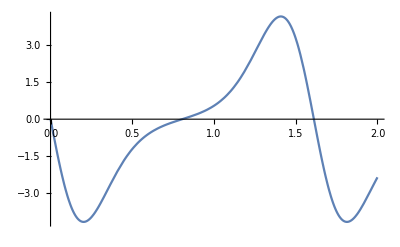

```mathematica
Plot[fi1'[x],{x,0,2}]
```

```mathematica
fi2[x_] = ArcCos[Log[2.5*x]/1.4]/3.9
```

0.25641 ArcCos[0.714286 Log[2.5 x]]

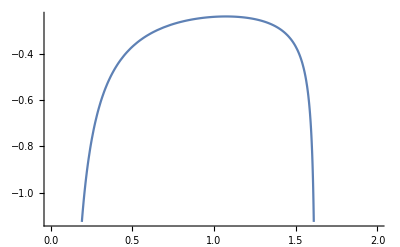

```mathematica
Plot[fi2'[x],{x,0,2}]
```

```mathematica
fi2'[1.5]
```

-0.370419